```mathematica
Efunc[μ_,Γ_,a_,x_]:=ⅇ^(-x^2/(2μ))∑_(s=-∞)^∞ DiracDelta[x-(s+a)Γ];
Efunct[μ_,Γ_,a_,x_](:=)^(-x^2/(2μ))∑_(s=-∞)^∞ ⅇ^(2π ⅈ a s)DiracDelta[x-s Γ];
Gauss[v_,x_]:=1/(√(2π v))ⅇ^(-x^2/(2v));
Θ[a_,b_,z_,τ_]:=Exp[π ⅈ τ a^2 + 2π ⅈ a (z+b)]EllipticTheta[3,π(z+ τ a + b), Exp[π ⅈ τ]];
αd[d_]:=√((2π)/d);
Λ[vq_,vp_]:=1-4vq vp;
norm[vq_,vp_,Γ_,j_,d_]:=Re[Θ[j/d,0,0,(2ⅈ Γ^2)/π  vp^2/Λ[vq,vp]]Θ[0,0,0, (2π ⅈ)/Γ^2 vq^2/Λ[vq,vp]]+Θ[j/d+1/2,0,0,(2ⅈ Γ^2)/π  vp^2/Λ[vq,vp]]Θ[0,1/2,0, (2π ⅈ)/Γ^2 vq^2/Λ[vq,vp]]];
```

```mathematica
EconvG[μ_,Γ_,a_,v_,x_]:= Gauss[v,x]Θ[a,0,(Γ x)/(2 π ⅈ v),(ⅈ Γ^2 (1+v/μ))/(2 π v)];

EtconvG[μ_,Γ_,a_,v_,x_]:= Gauss[v,x]Θ[0,a,(ⅈ Γ x)/(2 π v),(ⅈ Γ^2)/(2 π v)];
```

Note : σ^2 = 0.5 means 0 squeezing so 0 < σ^2 (variance) < 0.5

```mathematica
ProductTerm[q_,p_,d_,i_,j_,vq_,vp_,Γ_,parity_]:=Chop[EconvG[Λ[vq,vp]/(4vp),Γ,(i+j)/(2d)+parity/2,vq,q]]Chop[EtconvG[Λ[vq,vp]/(4vq),(π Λ[vq,vp])/Γ,(i-j)/(2d)+parity/2,vp,p]];
Wigner[q_,p_,d_,i_,j_,vq_,vp_,Γ_]:=1/(√(norm[vq,vp,Γ,i,d]norm[vq,vp,Γ,j,d]))Chop[ProductTerm[q,p,d,i,j,vq,vp,Γ,0]+ProductTerm[q,p,d,i,j,vq,vp,Γ,1]];
```

For symmetric case vq=vp=v, Γ = α_d d √Λ (Section 5. from Ref.)

```mathematica
ClearAll[mat,limits,range,vq,vp,d,Γ];
limits=2;
range=60;
vq = vp = 0.02;
d=2;
Γ =αd[d] d √Λ[vq,vp];
```

```mathematica
(* Density Plot - slow *)
Quiet[DensityPlot[Wigner[√π(q),√π(p),d,1,1,vq,vp,Γ],{q,-limits,limits},{p,-limits,limits},PlotPoints->60,ColorFunction->"RedBlueTones",ColorFunctionScaling->True,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]]
```

$Aborted

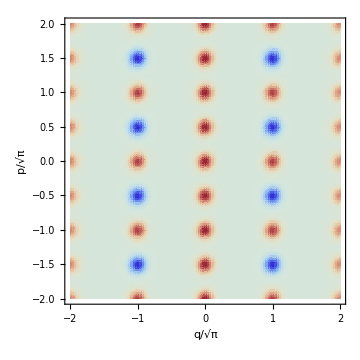

```mathematica
(* List Desnity Plot - fast *) 
Quiet[
mat=Table[Re[Chop[Wigner[√π((x-1)(limits/range)-limits),√π((p-1)(limits/range)-limits),d,0,0,vq,vp,Γ]]],{p,1,2 range +1},{x,1,2 range +1}];
];
mat=mat/(1+0Abs[Total[mat,2]](limits/range)^2);
plot=ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]
```